```mathematica
SetDirectory["/home/dschiebe/Documents/lanayru/PhD_Files/HexaBox_102PureIntsDone"];
PureIntegralsOld=ReadList[FileNameJoin[{Directory[],"files/PureIntegralBasis1-119.txt"}]];
PureIntegralsNew=PureIntegralsOld;
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
$P=2^31-1;
$P=2^31-1;
CayleyEntry[i_,j_]:=Module[{mat},
If[i==0 && j==0 ,
Return[0];
];
If[i==0 || j==0 ,
Return[1];
];

If[i==j,
mat=2msq[i]/.intMasses;
Return[mat];
];
If[i<j,
mat=((msq[i]/.intMasses)+(msq[j]/.intMasses)-Expand[(Sum[q[n],{n,i,j-1}])^2])/.mandelstamScalarProducts/.kinematics;
Return[mat];
];
If[i>j,
mat=CayleyEntry[j,i];
Return[mat];
];
]
cutCayley[mat_,l_]:=Module[{res},
res=mat;
res=Delete[res,l];
res=Transpose[Delete[Transpose[res],l]];
res
]
```

{hxb[-1,1,0,1,0,1,0,1,0,0,0,0,0],hxb[0,1,0,1,0,1,0,1,0,0,0,0,0],hxb[1,0,0,1,0,1,0,1,-1,0,0,0,0],hxb[1,0,0,1,0,1,0,1,0,0,0,0,0]}

{123,141,158,159}

# Diagram 158/159 (Basis1-119)

hxb[1,0,0,1,0,1,0,1,-1,0,0,0,0]

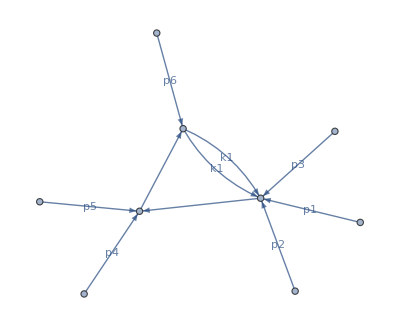

```mathematica
PureIntegralsNew[[158]]
plotDiagram[PureIntegralsNew[[158]]]
```

```mathematica
q[1]=p[5]+p[4]/.p4cons;
q[2]=p[1]+p[2]+p[3];
q[3]=-q[1]-q[2];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
convchange={v23->Expand[2 p[5]p[4]]/.mandelstamScalarProducts/.kinematics,q2->0,v45->s123};
BasisChange[1]=ep^3/LS*1/PR[1]
BasisChange[2]=ep^2((1-2ep)(q2+mt2+v23)/PR[8]-ep(q2+v23+v45)1/(2 PR[1]))/.convchange
```

(0 | 1 | 1 | 1
1 | 2 mt2 | mt2-s45 | 0
1 | mt2-s45 | 0 | -s123
1 | 0 | -s123 | 0)

1/(2 root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2])

(2 ep^3 root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2])/PR[1]

ep^2 (-(ep (-mt2+s123+s45))/(2 PR[1])+((1-2 ep) s45)/PR[8])

# Diagram 123/141 (Basis1-119)

hxb[-1,1,0,1,0,1,0,1,0,0,0,0,0]

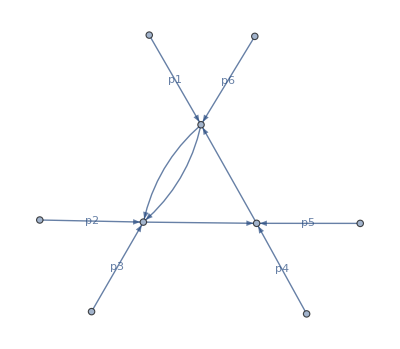

```mathematica
PureIntegralsNew[[123]]
plotDiagram[PureIntegralsNew[[123]]]
```

```mathematica
q[1]=p[2]+p[3]/.p4cons;
q[2]=p[4]+p[5];
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->0,msq[3]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
convchange={v23->Expand[2 p[5]p[4]]/.mandelstamScalarProducts/.kinematics,q2->0,v45->s123};
BasisChange[3]=ep^3/LS*1/PR[2]
BasisChange[4]=ep^2((1-2ep)(q2+mt2+v23)/PR[8]-ep(q2+v23+v45)1/(2 PR[2]))/.convchange/.{s123->s23}
BasisChange[4]=ep^2 (-(ep (-s16+s23+s45))/(2 PR[2])+((1-2 ep) s45)/PR[8])
```

(0 | 1 | 1 | 1
1 | 0 | -s23 | mt2-s16
1 | -s23 | 0 | mt2-s45
1 | mt2-s16 | mt2-s45 | 2 mt2)

1/(2 root[s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2])

(2 ep^3 root[s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2])/PR[2]

ep^2 (-(ep (-mt2+s23+s45))/(2 PR[2])+((1-2 ep) s45)/PR[8])

ep^2 (-(ep (-s16+s23+s45))/(2 PR[2])+((1-2 ep) s45)/PR[8])

# Diagram 139 (Basis1-119)

hxb[0,0,1,1,0,1,1,1,0,0,0,0,0]

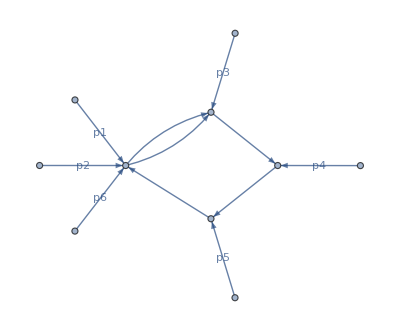

```mathematica
PureIntegralsOld[[139]]
plotDiagram[PureIntegralsOld[[139]]]
```

```mathematica
BasisChange[5]=Factor[Expand[-2 ep^3(2*p[4]p[5]) (2ep-1) /.kinematics/.mandelstamScalarProducts]]
```

2 ep^3 (-1+2 ep) (mt2-s45)

# Diagram 143 (Basis1-119)

hxb[0,1,0,1,0,1,1,1,0,0,0,0,0]

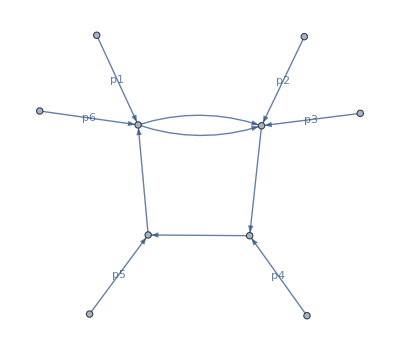

```mathematica
PureIntegralsOld[[143]]
plotDiagram[PureIntegralsOld[[143]]]
```

```mathematica
BasisChange[6]=Factor[Expand[-2 ep^3(2*p[4]p[5]) (2ep-1) /.kinematics/.mandelstamScalarProducts]];
BasisChange[6]=2 ep^3 (-1+2 ep) (mt2-s45)
```

2 ep^3 (-1+2 ep) (mt2-s45)

# Diagram 147 (Basis1-119)

hxb[0,1,0,1,1,1,0,1,0,0,0,0,0]

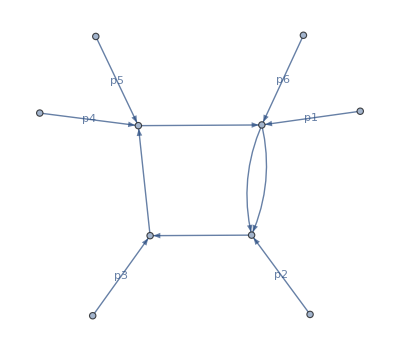

```mathematica
PureIntegralsOld[[147]]
plotDiagram[PureIntegralsOld[[147]]]
```

```mathematica
BasisChange[7]=Factor[Expand[Expand[-2 ep^3(2*p[3](p[4]+p[5])) (2ep-1) ]/.kinematics/.mandelstamScalarProducts]]
```

-2 ep^3 (-1+2 ep) (s345-s45)

# Diagram 160 (Basis1-119)

hxb[1,0,0,1,0,1,1,1,0,0,0,0,0]

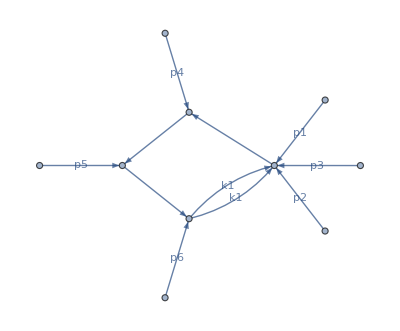

```mathematica
PureIntegralsOld[[160]]
plotDiagram[PureIntegralsOld[[160]]]
```

```mathematica
BasisChange[8]=2 ep^3 (-1+2 ep) (mt2-s45)
```

2 ep^3 (-1+2 ep) (mt2-s45)

# Diagram 163 (Basis1-119)

hxb[1,0,0,1,1,1,0,1,0,0,0,0,0]

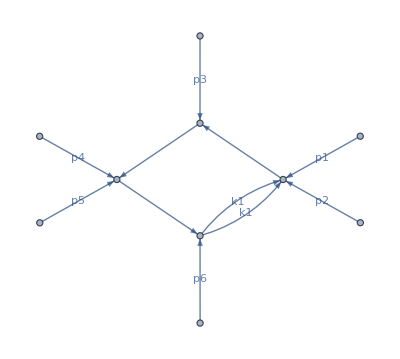

```mathematica
PureIntegralsOld[[163]]
plotDiagram[PureIntegralsOld[[163]]]
```

```mathematica
BasisChange[9]=2 ep^3 (-1+2 ep) (-s45+s345)
```

2 ep^3 (-1+2 ep) (s345-s45)

# Diagram 120/137 (Basis1 - 119)

hxb[-1,0,1,1,0,0,1,1,1,0,0,0,0]

hxb[0,0,1,1,0,0,1,1,1,0,0,0,0]

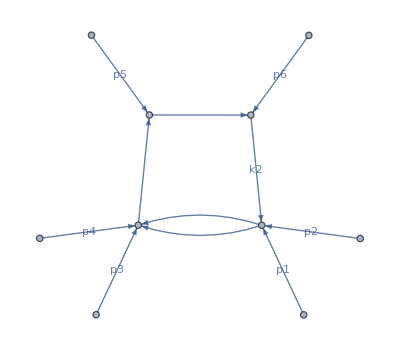

```mathematica
PureIntegralsOld[[120]]
PureIntegralsOld[[137]]
plotDiagram[PureIntegralsOld[[120]]]
```

```mathematica
q[1]=p[5]/.p4cons;
q[2]=p[4]+p[3]+p[1]+p[2];
q[3]=-q[1]-q[2];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[10]=ep^3/LS (1-2ep)
```

(0 | 1 | 1 | 1
1 | 2 mt2 | 0 | 0
1 | 0 | 0 | -s56
1 | 0 | -s56 | 0)

1/(2 root[-4 mt2 s56+s56^2])

2 (1-2 ep) ep^3 root[-4 mt2 s56+s56^2]

```mathematica
q[1]=p[4]+p[3]/.p4cons;
q[2]=p[1]+p[2];
q[3]=p[6]/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->0,msq[2]->0,msq[3]->0,msq[4]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[FullSimplify[x]]
BasisChange[11]=ep^3/LS 1/PR[3]
```

(0 | -s34 | -s56 | 0
-s34 | 0 | -s12 | mt2-s345
-s56 | -s12 | 0 | 0
0 | mt2-s345 | 0 | 2 mt2)

1/(2 root[s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56)])

(2 ep^3 root[s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56)])/PR[3]

# Diagram 121/138 (Basis1 - 119)

hxb[-1,0,1,1,0,1,0,1,1,0,0,0,0]

hxb[0,0,1,1,0,1,0,1,1,0,0,0,0]

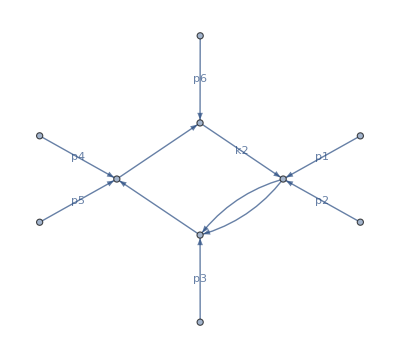

```mathematica
PureIntegralsOld[[121]]
PureIntegralsOld[[138]]
plotDiagram[PureIntegralsOld[[121]]]
```

```mathematica
q[1]=p[4]+p[5]/.p4cons;
q[2]=p[3]+p[1]+p[2];
q[3]=-q[1]-q[2];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[12]=ep^3/LS (1-2ep)
```

(0 | 1 | 1 | 1
1 | 2 mt2 | mt2-s45 | 0
1 | mt2-s45 | 0 | -s123
1 | 0 | -s123 | 0)

1/(2 root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2])

2 (1-2 ep) ep^3 root[mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2]

```mathematica
q[1]=p[4]+p[5]/.p4cons;
q[2]=p[3];
q[3]=p[1]+p[2]/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2]:>x
BasisChange[13]=ep^3/LS 1/PR[3]
```

(2 mt2 | mt2-s45 | mt2-s345 | 0
mt2-s45 | 0 | 0 | -s123
mt2-s345 | 0 | 0 | -s12
0 | -s123 | -s12 | 0)

1/(2 (mt2 s12-mt2 s123+s123 s345-s12 s45))

(2 ep^3 (mt2 s12-mt2 s123+s123 s345-s12 s45))/PR[3]

# Diagram 126/145 (Basis1 - 119)

hxb[-1,1,0,1,1,0,1,1,0,0,0,0,0]

hxb[0,1,0,1,1,0,1,1,0,0,0,0,0]

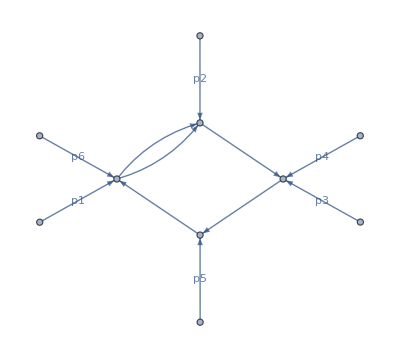

```mathematica
PureIntegralsOld[[126]]
PureIntegralsOld[[145]]
plotDiagram[PureIntegralsOld[[126]]]
```

```mathematica
q[1]=p[1]+p[2]+p[6]/.p4cons;
q[2]=p[5]/.p4cons;
q[3]=-q[1]-q[2];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[14]=ep^3/LS (1-2ep)

q[1]=p[5]/.p4cons;
q[2]=p[3]+p[4];
q[3]=p[2]/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2]:>x
BasisChange[15]=ep^3/LS 1/PR[2]
```

(0 | 1 | 1 | 1
1 | 2 mt2 | mt2-s345 | mt2-s34
1 | mt2-s345 | 0 | -mt2
1 | mt2-s34 | -mt2 | 0)

1/(2 root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2])

2 (1-2 ep) ep^3 root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2]

(2 mt2 | 0 | mt2-s345 | mt2-s16
0 | 0 | -s34 | -s234
mt2-s345 | -s34 | 0 | 0
mt2-s16 | -s234 | 0 | 0)

1/(2 (mt2 s234-mt2 s34+s16 s34-s234 s345))

(2 ep^3 (mt2 s234-mt2 s34+s16 s34-s234 s345))/PR[2]

# Diagram 161/162 (Basis1 - 119)

hxb[1,0,0,1,1,0,1,1,-1,0,0,0,0]

hxb[1,0,0,1,1,0,1,1,0,0,0,0,0]

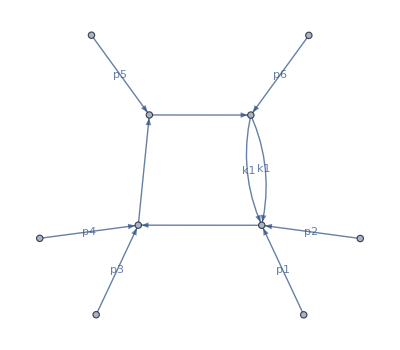

```mathematica
PureIntegralsOld[[161]]
PureIntegralsOld[[162]]
plotDiagram[PureIntegralsOld[[162]]]
```

```mathematica
q[1]=p[4]+p[3]/.p4cons;
q[2]=p[1]+p[2]+p[6]/.p4cons;
q[3]=-q[1]-q[2];
intMasses={msq[1]->0,msq[2]->0,msq[3]->mt2};
modcayleyMat=Table[CayleyEntry[i,j],{i,0,3},{j,0,3}];
modcayleyMat//MatrixForm
kP=3+1;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]
BasisChange[16]=ep^3/LS (1-2ep)

q[1]=p[5]/.p4cons;
q[2]=p[3]+p[4];
q[3]=p[2]+p[1]/.p4cons;
q[4]=-q[1]-q[2]-q[3];
intMasses={msq[1]->mt2,msq[2]->0,msq[3]->0,msq[4]->0};
modcayleyMat=Table[CayleyEntry[i,j],{i,1,4},{j,1,4}];
modcayleyMat//MatrixForm
kP=4;
LS=2^(-kP/2+1)/root[(-1)^Floor[kP/2] Det[modcayleyMat]]/.root[x_]:>root[Factor[x]]/.root[x_^2]:>x
BasisChange[17]=ep^3/LS 1/PR[1]
```

(0 | 1 | 1 | 1
1 | 0 | -s34 | 0
1 | -s34 | 0 | mt2-s345
1 | 0 | mt2-s345 | 2 mt2)

1/(2 root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2])

2 (1-2 ep) ep^3 root[mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2]

(2 mt2 | 0 | mt2-s345 | 0
0 | 0 | -s34 | -s56
mt2-s345 | -s34 | 0 | -s12
0 | -s56 | -s12 | 0)

1/(2 root[s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56)])

(2 ep^3 root[s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56)])/PR[1]

# Assemble basis

```mathematica
SelectInts={7,8,9,10,11,12,14,15,16,17,21,24,75,76,77,78,79,81,82,83,84,112,113,114,115,158,159,123,141,139,143,147,160,163,120,137,121,138,126,145,161,162};
SelectIntsNotPure=Pick[SelectInts,Thread[SelectInts>119]]
SelectIntsPure=Pick[SelectInts,Thread[SelectInts<=119]]

PureIntegralsNew[[158]]=Collect[PureIntegralsOld[[159]]*BasisChange[1]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[159]]=Collect[PureIntegralsOld[[159]]*BasisChange[2]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[123]]=Collect[PureIntegralsOld[[141]]*BasisChange[3]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[141]]=Collect[PureIntegralsOld[[141]]*BasisChange[4]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[139]]=Collect[PureIntegralsOld[[139]]*BasisChange[5]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[143]]=Collect[PureIntegralsOld[[143]]*BasisChange[6]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[147]]=Collect[PureIntegralsOld[[147]]*BasisChange[7]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[160]]=Collect[PureIntegralsOld[[160]]*BasisChange[8]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[163]]=Collect[PureIntegralsOld[[163]]*BasisChange[9]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[120]]=Collect[PureIntegralsOld[[137]]*BasisChange[10]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[137]]=Collect[PureIntegralsOld[[137]]*BasisChange[11]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[121]]=Collect[PureIntegralsOld[[138]]*BasisChange[12]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[138]]=Collect[PureIntegralsOld[[138]]*BasisChange[13]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[126]]=Collect[PureIntegralsOld[[145]]*BasisChange[14]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[145]]=Collect[PureIntegralsOld[[145]]*BasisChange[15]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[161]]=Collect[PureIntegralsOld[[162]]*BasisChange[16]//Expand,{_hxb,root[___]},Together];
PureIntegralsNew[[162]]=Collect[PureIntegralsOld[[162]]*BasisChange[17]//Expand,{_hxb,root[___]},Together];
SubPureInts=PureIntegralsNew[[SelectInts]];
Newsqrts=(Cases[SubPureInts,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
Oldsqrts=(Cases[PureIntegralsOld,root[___],Infinity]//DeleteDuplicates)/.root[x_]:>x
sqrtSetNew=Join[Oldsqrts,Newsqrts]//DeleteDuplicates;
Export[FileNameJoin[{Directory[],"files/Roots.txt"}],sqrtSetNew];
Export[FileNameJoin[{NotebookDirectory[],"BubblePureInts.txt"}],SubPureInts];
```

{158,159,123,141,139,143,147,160,163,120,137,121,138,126,145,161,162}

{7,8,9,10,11,12,14,15,16,17,21,24,75,76,77,78,79,81,82,83,84,112,113,114,115}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 mt2 s12+(-mt2-s12+s345)^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,s16^2-2 s16 s23+s23^2-2 s16 s45-2 s23 s45+s45^2,s56 (-4 mt2 s12 s34+(mt2-s345)^2 s56),s56 (-4 mt2 s12 s34+mt2^2 s56-2 mt2 s345 s56+s345^2 s56)}

{(-s12+s34)^2-2 (s12+s34) s56+s56^2,-4 s12 s23 s34 (-s123+s23-s234+s56)+(-s12 s23+s12 s234-s123 s234+s123 s34-s23 s34+s23 s56)^2,-4 mt2 s12+(-mt2-s12+s345)^2,-4 mt2 s56+s56^2,mt2^2-2 mt2 s123+s123^2-2 mt2 s45-2 s123 s45+s45^2,mt2^2-2 mt2 s34+s34^2-2 mt2 s345-2 s34 s345+s345^2,-4 mt2 s12 s34 s56+mt2^2 s56^2-2 mt2 s345 s56^2+s345^2 s56^2,mt2^2 s12^2-2 mt2^2 s12 s123+mt2^2 s123^2-2 mt2^2 s12 s34+2 mt2^2 s123 s34+2 mt2 s12 s123 s34-2 mt2 s123^2 s34+mt2^2 s34^2-2 mt2 s123 s34^2+s123^2 s34^2+2 mt2 s12 s123 s345-2 mt2 s123^2 s345-2 mt2 s123 s34 s345-2 s123^2 s34 s345+s123^2 s345^2-2 mt2 s12^2 s45+2 mt2 s12 s123 s45+4 mt2 s12 s34 s45-2 mt2 s123 s34 s45+2 s12 s123 s34 s45-2 mt2 s34^2 s45-2 s123 s34^2 s45-2 s12 s123 s345 s45+2 s123 s34 s345 s45+s12^2 s45^2-2 s12 s34 s45^2+s34^2 s45^2-2 mt2 s12 s345 s56+2 mt2 s123 s345 s56-2 mt2 s34 s345 s56+2 s123 s34 s345 s56-2 s123 s345^2 s56+2 mt2 s12 s45 s56-2 mt2 s123 s45 s56+2 mt2 s34 s45 s56-4 s12 s34 s45 s56+2 s123 s34 s45 s56+2 s12 s345 s45 s56+2 s123 s345 s45 s56+2 s34 s345 s45 s56-2 s12 s45^2 s56-2 s34 s45^2 s56+s345^2 s56^2-2 s345 s45 s56^2+s45^2 s56^2,s345^2-2 s345 s45+s45^2,mt2^2-2 mt2 s16+s16^2-2 mt2 s234-2 s16 s234+s234^2}

```mathematica
StillNonPureInts=DeleteElements[PureIntegralsOld[[120;;]],PureIntegralsOld[[SelectIntsNotPure]]];
NewPureInts=PureIntegralsNew[[SelectIntsNotPure]];
NewBasis=Join[PureIntegralsNew[[;;119]],NewPureInts,StillNonPureInts]//EchoFunction[Length];
Export[FileNameJoin[{Directory[],"files/PureIntegralBasis1-136.txt"}],NewBasis];
```

241